# Data Based Stability Analysis

## For unidirectional tipping system

## Functions & Initializations

Functions need descriptions

```mathematica
StochTippingDataGen[A_,SpecificGraph_,d_,TippedNodes_,rm_,DriverNodes_,UValue_,Noise_,dt_,InitVal_,FinalTime_]:=(Module[{n,B,r,eq,GenData,a=-1,b=1,x0=0},

n=Length[A];
r= Table[0&,n];

t=.;

r[[TippedNodes]]=rm;
B=A;
Do[B[[i,Complement[VertexOutComponent[SpecificGraph,i,1],{i}]]]=UValue,{i,DriverNodes}];



eq=Table[ⅆSymbol["x"<>ToString[i]][t]==(r[[i]][t]+b*(Symbol["x"<>ToString[i]][t]-x0)+a*(Symbol["x"<>ToString[i]][t]-x0)^3+d*Sum[Sqrt[-b/a]*Transpose[A][[i,j]],{j,1,n,1}]+d*Sum[Transpose[B][[i,j]]*(Symbol["x"<>ToString[j]][t]-x0),{j,1,n,1}])ⅆt+Noise*ⅆSymbol["w"<>ToString[i]][t],{i,1,n,1}];



GenData=RandomFunction[ItoProcess[eq,Table[Symbol["x"<>ToString[k]][t],{k,1,n}],{Table[Symbol["x"<>ToString[k]],{k,1,n}],InitVal},t,Table[Symbol["w"<>ToString[k]]\[Distributed]WienerProcess[],{k,1,n}]],{0.,FinalTime,dt},Method->"KloedenPlatenSchurz"];

GenData=TemporalData[Table[GenData["Values"][[;;,l]],{l,1,n}],{0,FinalTime}];

GenData
]
)
(*this func is constructed for a=-1 and b=1 and x0=0.5 but we can probably change them
but same values for all nodes for now*)
(*We have the same problem of global variables x1, x2, ..*)
(*remember to check the equation for a=-1 and compute r from Rs*)
```

```mathematica
Clear[MakeWindow];
MakeWindow[Data_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO,TP},
TP=Length[Data];
WO=(1-Overlap)*WL;
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
(*{Lb,Hb}*)
Data[[Lb;;Hb]]
]
```

```mathematica
Window[TP_,WL_,Overlap_,l_]:=
Module[{Lb,Hb,WO},
(*TP=Length[Data];*)
WO=(1-Overlap)*WL;
Lb=1+((l-1)*WO);
Hb=(WL+((l-1)*WO));
{Lb,Hb}

]
```

```mathematica
TippingCoefsBasic[TimeSerieValues_,i_,dt_]:=(Module[{Y,Mat,Dim,TP,MatrixRowDef,MatrixRow,Coefs,CoefKeys},
Dim=Dimensions[Values[TimeSerieValues]];
TP=Dim[[2]];



CoefKeys=Join[{"\*SubscriptBox[R, "<>StringDelete[ToString[i]," "]<>"]"},Table["\*SubscriptBox[x, "<>StringDelete[ToString[j]," "]<>"]",{j,Keys[TimeSerieValues]}],{"\*SubscriptBox[x, "<>StringDelete[ToString[i]," "]<>"]"<>"^3"}];

MatrixRowDef=Join[{Table[1,TP]},Values[TimeSerieValues]];

MatrixRow=Join[MatrixRowDef,{TimeSerieValues[i]^3}];

Mat=Join[Table[MatrixRow.MatrixRowDef[[k]]/TP,{k,1,Dim[[1]]+1}],{MatrixRow.TimeSerieValues[i]^2/TP}];

Y=Join[Table[(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).MatrixRowDef[[k]][[;;-2]]/(TP-1),{k,1,Dim[[1]]+1}],{(TimeSerieValues[i][[2;;]]-TimeSerieValues[i][[;;-2]]).TimeSerieValues[i][[;;-2]]^2/(TP-1)}];

Coefs=Association[Table[CoefKeys[[h]]->(LinearSolve[Mat,Y]/dt)[[h]],{h,1,Dim[[1]]+2}]];

Dataset[Coefs]
]
)
```

```mathematica
TippingCoefsWithWindow[TimeSerieValues_,i_,l_,dt_,WL_,Overlap_]:=(Module[{WindowTimeSerieValues,WindowTimeSerieValuesShuffle,Coefs,Errors,CoefsAfterError},

WindowTimeSerieValues=(MakeWindow[#,WL,Overlap,l]&)/@TimeSerieValues;

Coefs=TippingCoefsBasic[WindowTimeSerieValues,i,dt];

Coefs
]
)
```

```mathematica
NFixedPointsAndEigenValuesComplete[FixedPointEquations_,JacobianEquations_,n_]:=(Module[{FixedPoints,FixedPointsRules,EigenValues,StableFixedPointIndicies,UnStableFixedPointIndicies},
(**)

FixedPointsRules=NSolve[FixedPointEquations,Table[Indexed[x,i],{i,1,n}],Reals];
FixedPoints=Table[Indexed[x,i],{i,1,n}]/.FixedPointsRules;
EigenValues=Map[Eigenvalues][JacobianEquations/.FixedPointsRules];
StableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[And,Map[(#<0&),#],{0}]&),1];
UnStableFixedPointIndicies=Position[Re[EigenValues],__?(Apply[Or,Map[(#≥0&),#],{0}]&),1];
{{Length[FixedPoints],EigenValues,FixedPoints},{Length[Extract[FixedPoints,StableFixedPointIndicies]],Extract[EigenValues,StableFixedPointIndicies],Extract[FixedPoints,StableFixedPointIndicies]},{Length[Extract[FixedPoints,UnStableFixedPointIndicies]],Extract[EigenValues,UnStableFixedPointIndicies],Extract[FixedPoints,UnStableFixedPointIndicies]}}

]
)(*This is changed to get n*)
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
ConfigureMaTeX[
"pdfLaTeX"->"C:\\texlive\\2017\\bin\\win32\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.02.1\\bin\\gswin64c.exe"
];
```

## Data Generation

### r_{1} Sigmoid Function

```mathematica
5000/2/100
```

25

```mathematica
rSigmoid[t_]:=0.79(1-(1/(1+Exp[-t/100+Tf/2/100])))
```

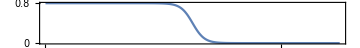

```mathematica
grsig=Plot[rSigmoid[t],{t,0,Tf},Frame->True,
FrameTicks->{{{0.8,0},None},{{0,2000,4000,{5000,MaTeX["t_c",FontSize->10],0.12,Directive[Dashed,Orange]},6000,8000,10000},None}},FrameTicksStyle->Directive[FontFamily->"Times",12,Black],
ImageSize->Medium,
AspectRatio->1/8.5,
(*PlotLabel->Style["C",12,FontFamily->"Times"],*)
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["r_1",FontSize->12]}]
```

```mathematica
Export[NotebookDirectory[]<>"r_simoidfunction_5000.txt",Transpose@Table[rSigmoid[t],{t,0,5000}]]
```

C:\Users\alish\Desktop\stability paper\r_simoidfunction_5000.txt

```mathematica
(*Export[NotebookDirectory[]<>"t_simoidfunction_5000.txt",Transpose@Range[0,5000]]*)
```

C:\Users\alish\Desktop\exploring stability project\t_simoidfunction_5000.txt

```mathematica
Export[NotebookDirectory[]<>"r_Sigmoid.pdf",grsig]
```

C:\Users\alish\Desktop\stability paper\r_Sigmoid.pdf

### Data

Noise = sqrt(0.5), dt = 0.005, Tf = 10000

```mathematica
Tf=5000;
SeedRandom[859];
Noise=Sqrt[0.5];(*Noise is larger than convergence tests*)
dt=0.005;
GenData=StochTippingDataGen[{{0,1},{0,0}},AdjacencyGraph[{{0,1},{0,0}}],0.3,{1},rSigmoid,{1},1,Noise,dt,{1.27,1.24},Tf](*Tf if 5000*)
```

TemporalData[<<2>>]

```mathematica
Floor[Tf/dt]
```

1000000

```mathematica
TimeSerieValues=<|"1"->GenData["ValueList"][[1]],"2"->GenData["ValueList"][[2]]|>;
```

```mathematica
(*Mean/@GenData["ValueList"]*)
```

```mathematica
(*g1=ListPlot[GenData["Paths"][[1]][[;;;;1]],PlotRange->All,ImageSize->Large,AspectRatio->1/8.5,PlotLabel->Style["A",FontFamily->"Times",12],Axes->False,Frame->True,FrameTicks->{{{-1,1},None},{Table[i,{i,0,5000,1000}],None}},FrameTicksStyle->Directive[FontFamily->"Times",12],FrameLabel->{None,Style[,12]},PlotStyle->{Thickness[0.002],Black},Joined->True]*)
```

```mathematica
gx1=ListPlot[GenData["Paths"][[1]],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/8.5,
(*PlotLabel->Style["A",FontFamily->"Times",12],*)
Axes->False,
Frame->True,
FrameTicks->{{{-1,1},None},{Range[0,5000,1000],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["x_1",FontSize->12]},
PlotStyle->{Thickness[0.002],Black},
Joined->True]
```

```mathematica
gx2=ListPlot[GenData["Paths"][[2]],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/8.5,
(*PlotLabel->Style["A",FontFamily->"Times",12],*)
Axes->False,
Frame->True,
FrameTicks->{{{-1,1},None},{Range[0,5000,1000],None}},
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["x_2",FontSize->12]},
PlotStyle->{Thickness[0.002],Black},
Joined->True]
```

```mathematica
(*Export[NotebookDirectory[]<>"x1_timeserie_5000_0.005_0.5.pdf",gx1]*)
```

C:\Users\alish\Desktop\stability paper\x1_timeserie_5000_0.005_0.5.pdf

```mathematica
(*Export[NotebookDirectory[]<>"x2_timeserie_5000_0.005_0.5.pdf",gx2]*)
```

C:\Users\alish\Desktop\stability paper\x2_timeserie_5000_0.005_0.5.pdf

```mathematica
(*Export[NotebookDirectory[]<>"x1_timeserie_5000_0.005_0.5.txt",GenData["Paths"][[1]],"Table","FieldSeparators"->Tab]*)
```

C:\Users\alish\Desktop\stability paper\x1_timeserie_5000_0.005_0.5.txt

```mathematica
(*Export[NotebookDirectory[]<>"x2_timeserie_5000_0.005_0.5.txt",GenData["Paths"][[2]],"Table","FieldSeparators"->Tab]*)
```

C:\Users\alish\Desktop\stability paper\x2_timeserie_5000_0.005_0.5.txt

### Windowing

Window Size 500000, Overlap = 95%

```mathematica
WinSize=500000;
Overlap=95/100;
```

```mathematica
MN=With[{TP=Floor[Tf/dt],Overlap=Overlap,WL=WinSize},(TP-(Overlap*WL))/((1-Overlap)*WL)]
```

21

## Cefficients

```mathematica
X1Coeffs=Table[Values@Normal[TippingCoefsWithWindow[TimeSerieValues,"1",l,dt,WinSize,Overlap]],{l,1,MN}]
```

{{0.665837,1.08375,0.0164854,-1.01215},{0.512193,1.2095,0.0447724,-1.03335},{0.427299,1.19667,0.0741247,-1.01455},{0.322447,1.27991,0.0799686,-1.02268},{0.302607,1.20529,0.0878354,-0.984029},{0.281005,1.15775,0.0817149,-0.954252},{0.246153,1.14344,0.0875297,-0.940029},{0.226487,1.13503,0.072234,-0.924433},{0.201902,1.08243,0.0789945,-0.894676},{0.191826,0.995536,0.0719151,-0.844953},{0.176246,0.926869,0.0668696,-0.806994},{0.154195,0.848018,0.0688128,-0.760194},{0.140276,0.763278,0.0602803,-0.713589},{0.129037,0.741125,0.0555212,-0.708537},{0.109813,0.696035,0.050029,-0.6869},{0.102272,0.693969,0.0436829,-0.701618},{0.0932352,0.676477,0.0366714,-0.7023},{0.067487,0.625163,0.0327228,-0.674966},{0.0433656,0.613474,0.0275937,-0.683417},{0.0231225,0.640795,0.0219709,-0.723322},{0.00693016,0.748563,0.0200543,-0.818838}}

```mathematica
X2Coeffs=Table[Values@Normal[TippingCoefsWithWindow[TimeSerieValues,"2",l,dt,WinSize,Overlap]],{l,1,MN}]
```

{{0.339223,0.320728,0.866513,-0.959806},{0.307927,0.322185,0.930831,-0.984521},{0.295032,0.328086,0.920665,-0.97499},{0.337413,0.294712,0.920453,-0.976147},{0.310789,0.285642,0.974969,-0.987686},{0.283744,0.27982,1.03958,-1.00738},{0.274157,0.28705,1.0611,-1.01679},{0.285399,0.281074,1.05638,-1.01686},{0.277984,0.28358,1.06061,-1.01575},{0.281173,0.283906,1.05904,-1.02085},{0.28913,0.285452,1.03806,-1.00923},{0.284965,0.288045,1.0344,-1.00628},{0.287452,0.291966,1.02684,-1.00435},{0.286622,0.282556,1.01349,-0.992602},{0.288355,0.273003,1.0196,-0.993687},{0.291939,0.281153,1.04693,-1.01688},{0.295542,0.283565,1.01568,-1.0011},{0.285253,0.288415,1.01417,-0.994931},{0.290508,0.293948,1.00004,-0.990727},{0.290025,0.291533,0.988701,-0.983125},{0.29105,0.287828,0.973571,-0.977006}}

```mathematica
Coeffs=MapThread[List,{X1Coeffs,X2Coeffs}];
```

## Data Based Stability Analysis

## Fixed Points & Eigen Values Computation

```mathematica
FixedPointEquationsWin=With[{n=2},Table[Table[Coeffs[[l,i]][[1]]+Sum[Coeffs[[l,i]][[j+1]]Indexed[x,j],{j,1,n}]+Coeffs[[l,i,n+2]]Indexed[x,i]^3==0,{i,1,n}],{l,1,MN}]];
```

```mathematica
JacobianEquationsWin=With[{n=2},Table[D[Table[Coeffs[[l,i]][[1]]+Sum[Coeffs[[l,i]][[j+1]]Indexed[x,j],{j,1,n}]+Coeffs[[l,i,n+2]]Indexed[x,i]^3,{i,1,n}],{Table[Indexed[x,i],{i,1,n,1}]}],{l,1,MN}]];
```

```mathematica
(*fr=NSolve[FixedPointEquations[[1]],Table[Indexed[x,i],{i,1,2}],Reals]*)
```

```mathematica
(*JacobianEquations[[1]]/.fr*)
```

```mathematica
(*With[{l=8},With[{DyData=(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l]},DyData[[2,3]]]]*)
```

```mathematica
StableFixedPointsWindows=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l][[2,3]],{l,1,MN}]
```

{{{1.26719,1.23722}},{{1.26656,1.23809},{-0.751566,-0.934876}},{{1.25927,1.23744},{-0.885304,-0.969247}},{{1.25673,1.23664},{-1.00587,-0.947982},{-0.902768,1.00771}},{{1.24884,1.23813},{-1.00274,-0.980802},{-0.877768,1.02302}},{{1.23954,1.23972},{-1.00314,-1.01439},{-0.882904,1.03306}},{{1.23382,1.2415},{-1.02709,-1.03116},{-0.906632,1.02805}},{{1.22736,1.24042},{-1.03343,-1.02164},{-0.938683,1.0293}},{{1.21858,1.24057},{-1.03933,-1.02965},{-0.933132,1.02809}},{{1.20575,1.23734},{-1.02029,-1.02252},{-0.913059,1.02874}},{{1.19083,1.23779},{-1.00754,-1.01345},{-0.900784,1.02926}},{{1.17608,1.2366},{-1.00245,-1.0157},{-0.883514,1.02829}},{{1.15348,1.23515},{-0.977673,-1.01016},{-0.860329,1.02835}},{{1.13632,1.23205},{-0.969157,-1.0041},{-0.860485,1.03127}},{{1.11242,1.22915},{-0.960563,-0.999897},{-0.85991,1.03828}},{{1.09207,1.22843},{-0.94937,-1.0025},{-0.863403,1.03739}},{{1.07096,1.2259},{-0.936364,-0.99214},{-0.864514,1.03121}},{{1.03903,1.22452},{-0.933335,-1.00161},{-0.868178,1.02639}},{{1.00494,1.22202},{-0.934243,-0.996648},{-0.882676,1.01987}},{{0.977982,1.21887},{-0.940235,-0.994683},{-0.903531,1.01603}},{{0.976392,1.21577},{-0.964661,-0.99129},{-0.937437,1.00897}}}

```mathematica
StableFixedPointsEigensWindows=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l][[2,2]],{l,1,MN}];
```

```mathematica
StableFixedPointsWindows[[;;,1]](*$$$$$$$$$$$$$*)
```

{{1.26719,1.23722},{1.26656,1.23809},{1.25927,1.23744},{1.25673,1.23664},{1.24884,1.23813},{1.23954,1.23972},{1.23382,1.2415},{1.22736,1.24042},{1.21858,1.24057},{1.20575,1.23734},{1.19083,1.23779},{1.17608,1.2366},{1.15348,1.23515},{1.13632,1.23205},{1.11242,1.22915},{1.09207,1.22843},{1.07096,1.2259},{1.03903,1.22452},{1.00494,1.22202},{0.977982,1.21887},{0.976392,1.21577}}

```mathematica
StableFixedPointsEigensWindows[[;;,1]]
```

{{-3.81166,-3.52153},{-3.82628,-3.53378},{-3.75403,-3.43402},{-3.71535,-3.40822},{-3.66246,-3.30361},{-3.65972,-3.1862},{-3.68723,-3.10288},{-3.66973,-3.01029},{-3.65877,-2.87353},{-3.65102,-2.66851},{-3.61791,-2.4891},{-3.59732,-2.29107},{-3.5816,-2.07328},{-3.51705,-1.99315},{-3.49256,-1.84572},{-3.56367,-1.80927},{-3.50368,-1.73416},{-3.46633,-1.55592},{-3.44253,-1.45298},{-3.39626,-1.4314},{-3.36206,-1.59007}}

```mathematica
LambdaMin=Min/@StableFixedPointsEigensWindows[[;;,1]];
```

```mathematica
LambdaMax=Max/@StableFixedPointsEigensWindows[[;;,1]]
```

{-3.52153,-3.53378,-3.43402,-3.40822,-3.30361,-3.1862,-3.10288,-3.01029,-2.87353,-2.66851,-2.4891,-2.29107,-2.07328,-1.99315,-1.84572,-1.80927,-1.73416,-1.55592,-1.45298,-1.4314,-1.59007}

```mathematica
LambdaMax={-3.5215254310856,-3.5337780526854337,-3.4340194776520847,-3.4082198562234676,-3.3036141207943754,-3.1861952320558644,-3.102882591236979,-3.0102889731931475,-2.873528918864827,-2.6685060782097643,-2.4890952496064602,-2.2910680791722537,-2.073275872668507,-1.9931519790880137,-1.8457160657678304,-1.8092707512939081,-1.734159389551391,-1.5559234392053043,-1.452983866386388,-1.4314018426633865,-1.43};
```

```mathematica
Ts=Table[(Plus@@(Window[Tf/dt,WinSize,Overlap,l])-1)/2,{l,1,MN}]*dt
```

{1250.,1375.,1500.,1625.,1750.,1875.,2000.,2125.,2250.,2375.,2500.,2625.,2750.,2875.,3000.,3125.,3250.,3375.,3500.,3625.,3750.}

```mathematica
Floor[Window[Floor[Tf/dt],WinSize,Overlap,1][[2]]*dt]
```

2500

```mathematica
Ts=Floor[Table[(Window[Floor[Tf/dt],WinSize,Overlap,l][[2]]),{l,1,MN}]*dt]
```

{2500,2625,2750,2875,3000,3125,3250,3375,3500,3625,3750,3875,4000,4125,4250,4375,4500,4625,4750,4875,5000,5125,5250,5375,5500,5625,5750,5875,6000,6125,6250,6375,6500,6625,6750,6875,7000,7125,7250,7375,7500,7625,7750,7875,8000,8125,8250,8375,8500,8625,8750,8875,9000,9125,9250,9375,9500,9625,9750,9875,10000}

```mathematica
Export[NotebookDirectory[]<>"EigenValuesMax.txt",Transpose@LambdaMax]
```

C:\Users\alish\Desktop\stability paper\EigenValuesMax.txt

```mathematica
Export[NotebookDirectory[]<>"EigenValuesMin.txt",Transpose@LambdaMin]
```

C:\Users\alish\Desktop\stability paper\EigenValuesMin.txt

```mathematica
(*Export[NotebookDirectory[]<>"t_Eigenvalues_5000.txt",Transpose@Ts]*)
```

C:\Users\alish\Desktop\exploring stability project\t_Eigenvalues_5000.txt

## Figures

```mathematica
leglambda=PointLegend[{Black,Red},{MaTeX["\\lambda_{min}",FontSize->10],MaTeX["\\lambda_{max}",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

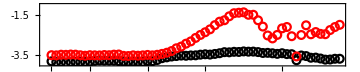

```mathematica
glambda=ListPlot[{MapThread[List,{Ts,(*1/Abs@*)LambdaMin}],MapThread[List,{Ts,(*1/Abs@*)LambdaMax}]},
Frame->True,
FrameTicks->{{Range[-3.5,-1.5,1],None},{{2500,3500,{5000,5000,0.2,Directive[Dashed,Orange]},6500,8500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{-4,-1}},
PlotLegends->Placed[leglambda,{0.2,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2Eigenvalue_sqrt0.5_500.pdf",glambda]
```

C:\Users\alish\Desktop\stability paper\2Eigenvalue_sqrt0.5_500.pdf

```mathematica
legtime=PointLegend[{Black,Red},{MaTeX["1/|\\lambda_{min}|",FontSize->10],MaTeX["1/|\\lambda_{max}|",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

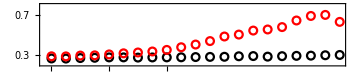

```mathematica
gtimescale=ListPlot[{MapThread[List,{Ts,1/Abs@LambdaMin}],MapThread[List,{Ts,1/Abs@LambdaMax}]},
Frame->True,
FrameTicks->{{Range[0.3,0.7,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{0.2,0.8}},
PlotLegends->Placed[legtime,{0.25,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2timescale_sqrt0.5_500.pdf",gtimescale]
```

C:\Users\alish\Desktop\stability paper\2timescale_sqrt0.5_500.pdf

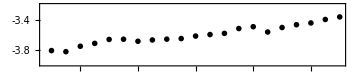

```mathematica
gmin=ListPlot[MapThread[List,{Ts,(*1/Abs@*)LambdaMin}],
Frame->True,
FrameTicks->{{Range[-3.8,-3.4,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{min}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{-4,-3.2}}]
```

```mathematica
Export[NotebookDirectory[]<>"min_Eigenvalue_sqrt0.5_500.pdf",gmin]
```

C:\Users\alish\Desktop\stability paper\min_Eigenvalue_sqrt0.5_500.pdf

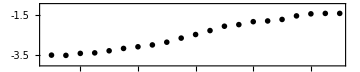

```mathematica
gmax=ListPlot[MapThread[List,{Ts,(*1/Abs@*)LambdaMax}],
Frame->True,
FrameTicks->{{Range[-3.5,-1.5,1],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda_{max}",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{-4,-1}}]
```

```mathematica
Export[NotebookDirectory[]<>"max_Eigenvalue_sqrt0.5_500.pdf",gmax]
```

C:\Users\alish\Desktop\stability paper\max_Eigenvalue_sqrt0.5_500.pdf

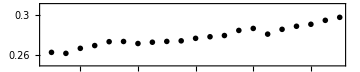

```mathematica
gtmin=ListPlot[MapThread[List,{Ts,1/Abs@LambdaMin}],
Frame->True,
FrameTicks->{{Range[0.26,0.30,0.02],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{min}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{0.25,0.31}}]
```

```mathematica
Export[NotebookDirectory[]<>"min_timescale_sqrt0.5_500.pdf",gtmin]
```

C:\Users\alish\Desktop\stability paper\min_timescale_sqrt0.5_500.pdf

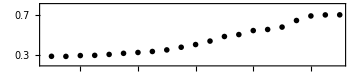

```mathematica
gtmax=ListPlot[MapThread[List,{Ts,1/Abs@LambdaMax}],
Frame->True,
FrameTicks->{{Range[0.3,0.7,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda_{max}|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->"OpenMarkers",
PlotStyle->{Black},
PlotRange->{Automatic,{0.2,0.8}}]
```

```mathematica
Export[NotebookDirectory[]<>"max_timescale_sqrt0.5_500.pdf",gtmax]
```

C:\Users\alish\Desktop\stability paper\max_timescale_sqrt0.5_500.pdf

## Figures and Data for Theory

```mathematica
AllrsFunc=Table[If[i==1,rSigmoid,0&],{i,1,2}](*node numbers and tipping node specification*)
```

{rSigmoid,0&}

```mathematica
graph=Graph[{1->2},VertexLabels->Automatic];
A=AdjacencyMatrix[graph]//Normal;
```

```mathematica
FixedPointEquationsWinTh=With[{n=2,d=0.3},Table[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,n}]-Indexed[x,i]^3+Indexed[x,i]==0,{i,1,n}],{t,0,5000,200}]];(*d=0.3, Tf(5000), nodes number(n)*)
```

```mathematica
JacobianEquationsWinTh=With[{n=2,d=0.5},Table[D[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,n}]-Indexed[x,i]^3+Indexed[x,i],{i,1,n}],{Table[Indexed[x,i],{i,1,n,1}]}],{t,0,5000,200}]];(*d=0.3, Tf(5000), nodes number(n)*)
```

```mathematica
TsTh=Table[t,{t,0,5000,200}]
```

{0,200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000}

```mathematica
(*With[{l=8},With[{DyData=(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[#]],JacobianEquationsWin[[#]],2])&[l]},DyData[[2,3]]]]*)
```

```mathematica
StableFixedPointsWindowsTh=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWinTh[[#]],JacobianEquationsWinTh[[#]],2])&[l][[2,3]],{l,1,26}]
```

{{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27302,1.24421}},{{1.27301,1.24421}},{{1.27299,1.24421}},{{1.27283,1.2442}},{{1.27165,1.2441}},{{1.26322,1.2434}},{{1.21469,1.23939}},{{-0.869238,-0.979776},{-0.869238,1.01907},{1.09289,1.22915}},{{-0.980712,-0.997094},{-0.980712,1.00288},{1.01823,1.22277}},{{-0.997346,-0.999602},{-0.997346,1.0004},{1.00263,1.22142}},{{-0.99964,-0.999946},{-0.99964,1.00005},{1.00036,1.22123}},{{-0.999951,-0.999993},{-0.999951,1.00001},{1.00005,1.2212}},{{-0.999993,-0.999999},{-0.999993,1.},{1.00001,1.2212}},{{-0.999999,-1.},{-0.999999,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}},{{-1.,-1.},{-1.,1.},{1.,1.2212}}}

```mathematica
StableFixedPointsEigensWindowsTh=Table[(NFixedPointsAndEigenValuesComplete[FixedPointEquationsWinTh[[#]],JacobianEquationsWinTh[[#]],2])&[l][[2,2]],{l,1,26}];
```

```mathematica
StableFixedPointsWindowsTh[[;;,1]](*$$$$$$$$$$$$$*)
```

{{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27302,1.24421},{1.27301,1.24421},{1.27299,1.24421},{1.27283,1.2442},{1.27165,1.2441},{1.26322,1.2434},{1.21469,1.23939},{-0.869238,-0.979776},{-0.980712,-0.997094},{-0.997346,-0.999602},{-0.99964,-0.999946},{-0.999951,-0.999993},{-0.999993,-0.999999},{-0.999999,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.},{-1.,-1.}}

```mathematica
StableFixedPointsEigensWindowsTh[[;;,1]]
```

{{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86172,-3.64419},{-3.86169,-3.64418},{-3.86153,-3.64417},{-3.86029,-3.64407},{-3.85125,-3.64334},{-3.78718,-3.63816},{-3.60823,-3.42638},{-1.87989,-1.26672},{-1.98259,-1.88539},{-1.99761,-1.9841},{-1.99968,-1.99784},{-1.99996,-1.99971},{-1.99999,-1.99996},{-2.,-1.99999},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.},{-2.,-2.}}

```mathematica
LambdaMinTh=Min/@StableFixedPointsEigensWindowsTh[[;;,1]];
```

```mathematica
LambdaMaxTh=Max/@StableFixedPointsEigensWindowsTh[[;;,1]];
```

```mathematica
TsTh=Range[0,5000,200]
```

{0,200,400,600,800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200,3400,3600,3800,4000,4200,4400,4600,4800,5000}

```mathematica
leglambda=PointLegend[{Black,Red},{MaTeX["\\lambda_{min}",FontSize->10],MaTeX["\\lambda_{max}",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

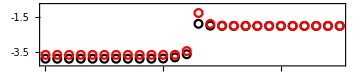

```mathematica
glambdaTheory=ListPlot[{MapThread[List,{TsTh,(*1/Abs@*)LambdaMinTh}],MapThread[List,{TsTh,(*1/Abs@*)LambdaMaxTh}]},
Frame->True,
FrameTicks->{{Range[-3.5,-1.5,1],None},{TsTh[[;;;;5]],None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["\\lambda",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{-4.2,-0.8}},
PlotLegends->Placed[leglambda,{0.2,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2Eigenvalue_Theory.pdf",glambdaTheory]
```

C:\Users\alish\Desktop\stability paper\2Eigenvalue_Theory.pdf

```mathematica
legtime=PointLegend[{Black,Red},{MaTeX["1/|\\lambda_{min}|",FontSize->10],MaTeX["1/|\\lambda_{max}|",FontSize->10]},LegendMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},LegendLayout->"Row"]
```

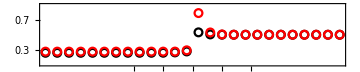

```mathematica
gtimescaleTheory=ListPlot[{MapThread[List,{TsTh,1/Abs@LambdaMinTh}],MapThread[List,{TsTh,1/Abs@LambdaMaxTh}]},
Frame->True,
FrameTicks->{{Range[0.3,0.7,0.2],None},{{1500,2000,{2500,2500,0.2,Directive[Dashed,Orange]},3000,3500},None}},
FrameTicksStyle->Directive[Black,10,FontFamily->"Times"],
FrameLabel->{MaTeX["t",FontSize->12],MaTeX["1/|\\lambda|",FontSize->12]},
AspectRatio->1/5,
ImageSize->Medium,
PlotMarkers->{{Graphics[Circle[]],Offset[8]},{Graphics[Circle[]],Offset[8]}},
PlotStyle->{Black,Red},
PlotRange->{Automatic,{0.1,0.9}},
PlotLegends->Placed[legtime,{0.25,0.8}]]
```

```mathematica
Export[NotebookDirectory[]<>"2timescale_Theory.pdf",glambdaTheory]
```

C:\Users\alish\Desktop\stability paper\2timescale_Theory.pdf

## Phase Portraits

### Data Based

#### First Window

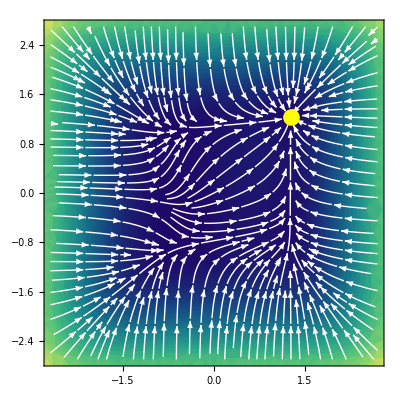

```mathematica
gfirstwin=With[{l=1},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),
StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_firstwin_500.pdf",gfirstwin]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_firstwin_500.pdf

#### Last Window

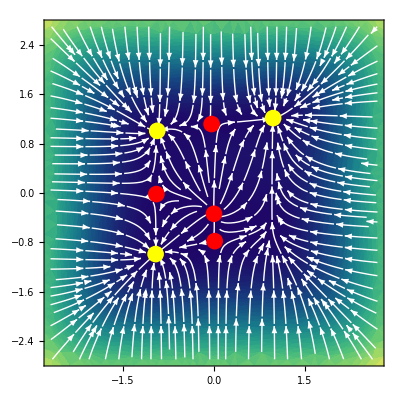

```mathematica
glastwin=With[{l=MN},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),
StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_lastwin_500.pdf",glastwin]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_lastwin_500.pdf

#### Animation

```mathematica
An=Manipulate[With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[FixedPointEquationsWin[[l]],JacobianEquationsWin[[l]],2]},
StreamDensityPlot[{Coeffs[[l,1]][[1]]+Coeffs[[l,1]][[2]]x+Coeffs[[l,1]][[3]]y+Coeffs[[l,1,2+2]]x^3,Coeffs[[l,2]][[1]]+Coeffs[[l,2]][[2]]x+Coeffs[[l,2]][[3]]y+Coeffs[[l,2,2+2]]y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BlueGreenYellow"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameLabel->{None,None,Style["",12],Style["",12]},StreamMarkers->"Arrow",StreamScale->0.1]],
{{l,1,Style["l",12]},1,31,1}]
```

```mathematica
Export[NotebookDirectory[]<>"Animate1.avi",An]
```

C:\Users\alish\Desktop\stability paper\Animate1.avi

### Theory

#### r = 0.79 t = 0

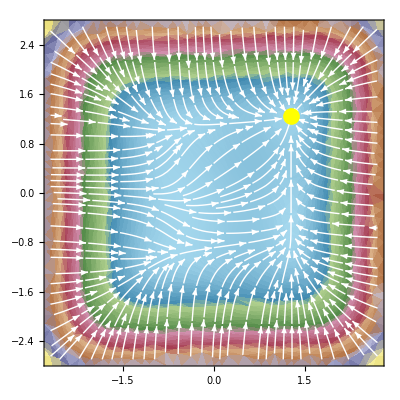

```mathematica
gfirstwinTh=With[{t=0,d=0.3},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i]==0,{i,1,2}],D[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i],{i,1,2}],{Table[Indexed[x,i],{i,1,2,1}]}],2]},
StreamDensityPlot[{rSigmoid[t]+x-x^3,d+d x+y-y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Yellow,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Red,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"DarkBands"(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*),
StreamColorFunction->None(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
StreamStyle->White,
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_firstwin_Theory.pdf",gfirstwinTh]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_firstwin_Theory.pdf

#### r = 0 t = 5000

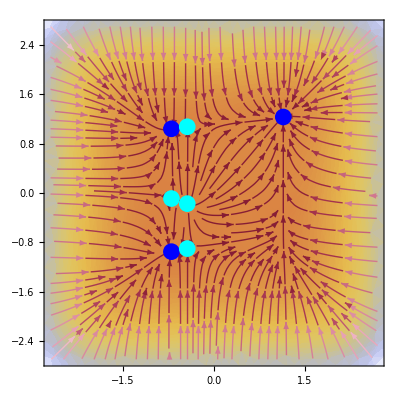

```mathematica
glastwinTh=With[{t=2520,d=0.3},With[{
FixedPointData=NFixedPointsAndEigenValuesComplete[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i]==0,{i,1,2}],D[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i],{i,1,2}],{Table[Indexed[x,i],{i,1,2,1}]}],2]},
StreamDensityPlot[{rSigmoid[t]+x-x^3,d+d x+y-y^3},{x,-2.7,2.7},{y,-2.7,2.7},Epilog->{{Blue,PointSize[0.03],Point[FixedPointData[[2,3]]]},{Cyan,PointSize[0.03],Point[FixedPointData[[3,3]]]}},ColorFunction->"BeachColors",(*ColorFunction->"Rainbow"*)(*Function[{x,y,vx,vy,n},Hue[n]]*)
StreamColorFunction->"ValentineTones"(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*),
(*StreamStyle->,*)
(*StreamColorFunction->"White"*)(*None*)(*Function[{x,y,vx,vy,n},(*ColorData[23][7]*)White]*)
(*StreamStyle->White*)
StreamPoints->Fine,
FrameTicksStyle->Directive[FontFamily->"Times",10,Black],
FrameLabel->{MaTeX["x_1",FontSize->12],MaTeX["x_2",FontSize->12],None,None},
StreamMarkers->"Arrow",StreamScale->0.1]]]
```

```mathematica
Export[NotebookDirectory[]<>"phaseportrait_lastwin_Theory.pdf",glastwinTh]
```

C:\Users\alish\Desktop\stability paper\phaseportrait_lastwin_Theory.pdf

```mathematica
With[{t=5000,d=0.3},NFixedPointsAndEigenValuesComplete[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i]==0,{i,1,2}],D[Table[AllrsFunc[[i]][t]+d Sum[A[[j,i]](Indexed[x,j]+1),{j,1,2}]-Indexed[x,i]^3+Indexed[x,i],{i,1,2}],{Table[Indexed[x,i],{i,1,2,1}]}],2][[1]]]
```

{7,{{-2.,-2.},{-2.,1.},{-2.,-2.},{1.,-0.855664},{1.,0.655367},{-2.7997,1.},{-3.47396,-2.}},{{-1.,-1.},{-1.,-1.64572×10^-12},{-1.,1.},{-1.09715×10^-11,-0.786483},{-1.09715×10^-11,-0.338936},{-1.09715×10^-11,1.12542},{1.,1.2212}}}

### Theory r = 0

#### d = 0.1

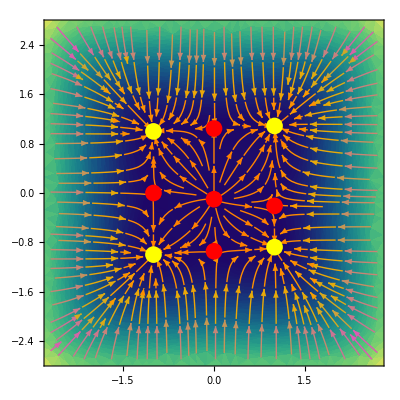

#### d = 0.3

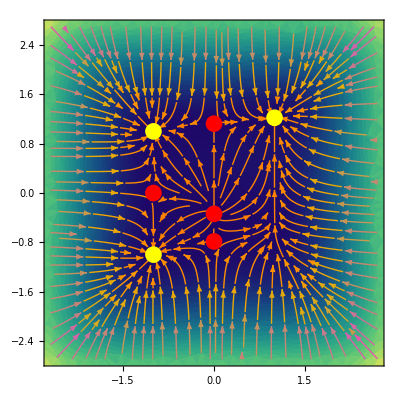

#### d = 1.5